```mathematica
fck:=25;
fcm:=fck+8;
gammac:=1.5;
alphacc:=.85;
fcd:=alphacc*fck/gammac;
Ecm:=Ceiling[22*10^3*(fcm/10)^(.3)];
fctm:=.3*fck^(2/3);
fctk005:=.7*fctm;
alphact:=alphacc;
fctd:=(alphact*fctk005)/gammac;
epsilonc2:=2/1000;
epsiloncu:=3.5/1000;
epsilonctu:=fctm/Ecm;
fyk:=450;
gammas:=1.15;
fyd:=fyk/gammas;
Es:=210*10^3;
epsilonse:=fyd/Es;
epsilonsu:=10/1000;
b:=350;
h:=350;
d1:=40;
d2:=40;
d:=h-d1;

As := 726*π;
A1s:=726*π;

NEd=0;
```

## Stato I: Prima fessurazione

```mathematica
x=.;
epsilonci=.;epsiloncs=.;epsilons=.;epsilon1s=.;
epsilonci:=epsilonctu;
epsiloncs[x_]:=(epsilonctu*x)/(h-x);
epsilons[x_]:=(epsilonctu*(d-x))/(h-x);
epsilon1s[x_]:=epsilonctu*(x-d1)/(h-x);
```

### Posizione dell’asse neutro x

```mathematica
g=NSolve[b*Integrate[fcd*(1-(1-epsilonctu/epsilonc2*y/(h-x))^2), {y,0,x}] + A1s*Es*epsilon1s[x] -As*Es*epsilons[x] - b*fctd*2/3*(h-x)==NEd && x>0, x, Reals];g
xI := x/. g[[1]];xI
```

{{x→180.083},{x→346.963},{x→7337.21}}

180.083

### Controllo deformazioni

```mathematica
epsilons[xI]*1000
```

0.0623061

```mathematica
epsilon1s[xI]*1000
```

0.0671818

```mathematica
epsiloncs[xI]*1000
```

0.0863652

#### Risultanti tensioni

Calcestruzzo compresso

```mathematica
Cc[x_]:=b*Integrate[fcd*(1-(1-epsilonctu/epsilonc2*y/(h-x))^2), {y, 0, x}];Cc[xI]
```

38003.3

Calcestruzzo teso

```mathematica
Tc[x_]:=b*fctd*2/3*(h-x);
```

Armatura compressa

```mathematica
Cs[x_]:= A1s*Es*epsilon1s[x];
```

Armatura tesa

```mathematica
Ts[x_]:=As*Es*epsilons[x];
```

#### Coefficiente λ e ψ

```mathematica
λ[x_]:=1/x*1/Cc[x] b*Integrate[fcd*(1-(1-epsilonctu/epsilonc2*y/(h-x))^2)*(x-y), {y, 0, x}]; λ[xI]
```

0.33455

```mathematica
ψ[x_]:=Cc[x]/(b*x*fcd);ψ[xI]
```

0.042561

### Momento resistente e curvatura

```mathematica
MRdI=Cc[xI]*(h/2-λ[xI]*xI)+Cs[xI]*(h/2-d2)+Ts[xI]*(d-h/2)+Tc[xI]*(h/2-((h-xI)/3));MRdI*10^-6
```

17.5083

```mathematica
χI=(epsiloncs[xI]-epsilons[xI])/d;χI
```

7.76098×10^-8

## Snervamento armature tese

La sezione è fessurata. Il calcestruzzo teso non dà contributo. Le armature tese sono snervate.

```mathematica
epsilon1s=.;epsilons=.;epsiloncs=.;epsilonci=.;
epsilons:=epsilonse;
epsilon1s[x_]:=epsilons/(d-x)(x-d2);
epsiloncs[x_]:=(epsilons*x)/(d-x);
```

### Posizione dell’asse neutro x

HP: σ’s = Es*ϵ’s -> campo elastico

```mathematica
g:=NSolve[b*Integrate[fcd*(1-(1-epsilons/epsilonc2*y/(d-x))^2), {y,0,x}] + A1s*Es*epsilon1s[x] -As*fyd==0 && x>0, x, Reals];g
xII:=x/.g[[1]];xII
```

{{x→137.996},{x→256.171}}

137.996

### Controllo deformazioni

```mathematica
epsilon1s[xII]*1000
```

1.06161

OK, armature superiori in campo elastico

```mathematica
epsiloncs[xII]*1000
```

1.49493

ϵ_c^s< ϵ_c2. Il parabola rettangolo non è completamente sviluppato. Non c’è la parte rettangolare

#### Risultanti tensioni

Calcestruzzo compresso

```mathematica
Cc[x_]:=b*Integrate[fcd*(1-(1-epsilons/epsilonc2*y/(d-x))^2), {y,0,x}];Cc[xII]
```

384011.

Armatura compressa

```mathematica
Cs[x_]:= A1s*Es*epsilon1s[x];
```

Armatura tesa

```mathematica
Ts[x_]:=As*fyd;
```

#### Coefficiente λ

```mathematica
λ[x_]:=1/x*1/Cc[x] b*Integrate[fcd*(1-(1-epsilons/epsilonc2*y/(d-x))^2)*(x-y),{y,0,x}]; λ[xII]
```

0.360986

```mathematica
ψ[xII]
```

0.561231

### Momento resistente e curvatura

```mathematica
MRdII=Cc[xI]*(h/2-λ[xII]*xII)+Cs[xII]*(h/2-d2)+Ts[xII]*(d-h/2);MRdII*10^-6
```

237.202

```mathematica
χII=Abs[(epsiloncs[xII]-epsilons)/d];χII
```

1.18845×10^-6

## Collasso

Si ipotizza che ϵ_c^s=ϵ_cu, e ϵ_s=ϵ_su con σ_s'=E_s ϵ_s'

```mathematica
epsilon1s=.;epsilons=.;epsiloncs=.;epsilonci=.;
epsilons:=epsilonsu;
epsilon1s[x_]:=epsilons/(d-x)(x-d2);
epsiloncs[x_]:=epsilonsu/(d-x)*x;
```

### Posizione dell’asse neutro x

HP armature superiori in campo elastico

```mathematica
g:=NSolve[b*.80952*x *fcd+ A1s*Es*epsilon1s[x] -As*fyd==0 && x>0, x, Reals];g
 xIII:=x/.g[[1]];xIII
```

{{x→70.483},{x→1655.15}}

70.483

### Controllo deformazioni

```mathematica
epsilon1s[xIII]*1000
```

1.27269

Le armature superiori in campo elastico

```mathematica
epsiloncs[xIII]*1000
```

2.94272

Il parabola rettangolo non è completamente sviluppato

```mathematica
ψ[x_]:=1-1/3*epsilonc2/epsiloncs[x];ψ[xIII]
```

0.773452

```mathematica
g:=NSolve[b*ψ[x]*x *fcd+ A1s*Es*epsilon1s[x] -As*fyd==0 && x>0, x, Reals]; g
xIII:=x/.g[[1]];xIII
```

{{x→70.483},{x→1655.14}}

70.483

```mathematica
epsilon1s[xIII]*1000
```

1.27269

```mathematica
epsiloncs[xIII]*1000
```

2.94271

OK, le ipotesi sono corrette.

#### Risultanti tensioni

Calcestruzzo compresso

```mathematica
Cc[x_]:=b*x*ψ[x]*fcd;Cc[xIII]
```

270304.

Armatura compressa

```mathematica
Cs[x_]:= A1s*Es*epsilon1s[x];Cs[xIII]
```

609575.

Armatura tesa

```mathematica
Ts[x_]:=As*fyd;Ts[xIII]
```

892485.

#### Coefficienti ψ e λ

ψ  e  di campo 2

```mathematica
λ[x_]:= (6*epsiloncs[x]^2-4*epsiloncs[x]*epsilonc2 + epsilonc2^2)/(4*epsiloncs[x]*(3*epsiloncs[x]-epsilonc2));λ[xIII]
```

0.403315

```mathematica
ψ[xIII]
```

0.773452

### Momento resistente e curvatura

```mathematica
MRdIII=Cc[xIII]*(h/2-λ[xIII]*xIII)+Cs[xIII]*(h/2-d2)+Ts[xIII]*(d-h/2);MRdIII*10^-6
```

242.397

```mathematica
χIII=Abs[(epsiloncs[xIII]-epsilons)/d];χIII
```

0.0000227654

```mathematica
N[χII]
```

1.18845×10^-6

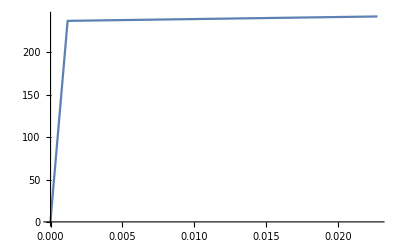

```mathematica
ListLinePlot[{{0,0},{χI*10^3, MRdI*10^-6},{χII*10^3, MRdII*10^-6}, {χIII*10^3, MRdIII*10^-6}}]
```

# N≠0

```mathematica
fck:=25;
fcm:=fck+8;
gammac:=1.5;
alphacc:=.85;
fcd:=alphacc*fck/gammac;
Ecm:=Ceiling[22*10^3*(fcm/10)^(.3)];
fctm:=.3*fck^(2/3);
fctk005:=.7*fctm;
alphact:=alphacc;
fctd:=(alphact*fctk005)/gammac;
epsilonc2:=2/1000;
epsiloncu:=3.5/1000;
epsilonctu:=.3*10^-3;
fyk:=450;
gammas:=1.15;
fyd:=fyk/gammas;
Es:=210*10^3;
epsilonse:=fyd/Es;
epsilonsu:=10/1000;
b:=350;
h:=350;
d1:=40;
d2:=40;
d:=h-d1;

As := 726*π;
A1s:=726*π;

NEd=1882*10^3;
```

```mathematica
x0[x_]:= epsiloncs[x]/epsilonc2*x;
```

## Stato I: Prima fessurazione

```mathematica
x=.;
epsilonci=.;epsiloncs=.;epsilons=.;epsilon1s=.;
epsilonci:=epsilonctu;
epsiloncs[x_]=(epsilonctu*x)/(h-x);
epsilons[x_]:=(epsilonctu*(d-x))/(h-x);
epsilon1s[x_]:=epsilonctu*(x-d1)/(h-x);
```

### Posizione dell’asse neutro x

HP: armature superiori e inferiori in campo elastico e parabola rettangolo non completamente sviluppato

```mathematica
g=NSolve[b*Integrate[fcd*(1-(1-epsilonctu/epsilonc2*y/(h-x))^2), {y,0,x}]+A1s*Es*epsilon1s[x]-As*Es*epsilons[x] - b*fctd*2/3*(h-x)==NEd && x>0, x, Reals];g
xI := x/. g[[1]];xI
```

{{x→306.105},{x→336.536}}

306.105

### Controllo deformazioni

```mathematica
epsilons[xI]*1000
```

0.0266187

```mathematica
epsilon1s[xI]*1000
```

1.81871

```mathematica
epsiloncs[xI]*1000
```

2.09209

ϵ_c > ϵ_c2

```mathematica
g=NSolve[b*Integrate[fcd*(1-(1-epsilonctu/epsilonc2*y/(h-x))^2), {y,0,x0[x]}]+ b*fcd*(x-x0[x])+A1s*Es*epsilon1s[x]-As*Es*epsilons[x] - b*fctd*2/3*(h-x)==NEd && x>0, x, Reals];g
xI := x/. g[[1]];xI
```

{{x→306.114},{x→317.837},{x→387.366},{x→420.926}}

306.114

### Controllo deformazioni

```mathematica
epsilons[xI]*1000
```

0.0265652

```mathematica
epsilon1s[xI]*1000
```

1.81912

```mathematica
epsiloncs[xI]*1000
```

2.09255

#### Risultanti tensioni

Calcestruzzo compresso

```mathematica
Cc[x_]:=b*Integrate[fcd*(1-(1-epsilonctu/epsilonc2*y/(h-x))^2), {y,0,x0[x]}]+ b*fcd*(x-x0[x]);Cc[xI]
```

1.03384×10^6

Calcestruzzo teso

```mathematica
Tc[x_]:=b*fctd*2/3*(h-x);Tc[xI]
```

10418.6

Armatura superiore compressa

```mathematica
Cs[x_]:= A1s*Es*epsilon1s[x];Cs[xI]
```

871299.

Armatura inferiore compressa

```mathematica
Ts[x_]:=As*Es*epsilons[x];Ts[xI]
```

12723.8

#### Coefficiente λ e ψ

```mathematica
x0[xI]
```

320.28

```mathematica
λ[x_]:=1/x*1/Cc[x]*((b*Integrate[fcd*(1-(1-epsilonctu/epsilonc2*y/(h-x))^2)*(x-y), {y,0,x0[x]}] )+b*Integrate[fcd*(x-y), {y,x0[x],x}]); λ[xI]
```

0.378103

```mathematica
ψ[x_]:=Cc[x]/(b*x*fcd);ψ[xI]
```

0.68114

### Momento resistente e curvatura

```mathematica
MRdI=Cc[xI]*(h/2-λ[xI]*xI)+Cs[xI]*(h/2-d2)+Ts[xI]*(d-h/2)+Tc[xI]*(h/2-((h-xI)/3));MRdI*10^-6
```

182.277

```mathematica
χI=Abs[(epsiloncs[xI]-epsilons[xI])/d];χI
```

6.66448×10^-6

## Snervamento armature

La sezione è fessurata. Il calcestruzzo teso non dà contributo. 
Suppongo che snervino le armature superiori

```mathematica
epsilon1s=.;epsilons=.;epsiloncs=.;epsilonci=.;
epsilon1s[x_]:=epsilonse;
epsiloncs[x_]:=epsilon1s[x]/(x-d2)*x;
epsilons[x_]:=epsilon1s[x]/(x-d2)*(d-x);
```

### Posizione dell’asse neutro x

```mathematica
x=.;
x0 [x_]:=epsilonc2/epsiloncs[x]*x
g=NSolve[b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2 y/x)^2), {y, 0, x}]+ A1s*fyd -As*Es*epsilons[x]==NEd  && x>0, x, Reals]; g
xII:=x/.g[[2]];xII
```

{{x→39.6182},{x→299.67}}

299.67

### Controllo deformazioni

```mathematica
epsilons[xII]*1000
```

0.0741259

```mathematica
epsiloncs[xII]*1000
```

2.15039

ϵ_c^s > ϵ_c2

```mathematica
x=.;
x0 [x_]:=epsilonc2/epsiloncs[x]*x
g=NSolve[b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2 y/x)^2), {y, 0, x0[x]}] + b*fcd*(x-x0[x])+ A1s*fyd -As*Es*epsilons[x]==NEd  && x>0, x, Reals]; g
xII:=x/.g[[1]];xII
```

{{x→299.641}}

299.641

### Controllo deformazioni

```mathematica
epsilons[xII]*1000
```

0.0743422

```mathematica
epsiloncs[xII]*1000
```

2.15042

#### Risultanti tensioni

Calcestruzzo compresso

```mathematica
Cc[x_]:=b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2 y/x)^2), {y, 0, x0[x]}] + b*fcd*(x-x0[x]);Cc[xII]
```

1.02512×10^6

Armatura compressa

```mathematica
Cs[x_]:= A1s*fyd;
```

Armatura tesa

```mathematica
Ts[x_]:=As*Es*epsilons[x];
```

#### Coefficiente λ

```mathematica
λ[x_]:=1/x*1/Cc[x]*(b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2*y/x)^2)*(x-y),{y, 0,x0[x]}] + b*Integrate[fcd*(x-y), {y, x0[x], x}]); λ[xII]
```

0.379815

```mathematica
ψ[x_]:=Cc[x]/(b*x*fcd);ψ[xII]
```

0.689983

### Momento resistente e curvatura

```mathematica
MRdII=Cc[xII]*(h/2-λ[xII]*xII)+Cs[xII]*(h/2-d2)+Ts[xII]*(d-h/2);MRdII*10^-6
```

188.022

```mathematica
χII=Abs[(epsiloncs[xII]+epsilons[xII])/d];χII
```

7.17665×10^-6

## Collasso

Si ipotizza che ϵ_c^s=ϵ_cu, e ϵ'_s=ϵ_su con σ_s=E_s ϵ_s

```mathematica
epsilon1s=.;epsilons=.;epsiloncs=.;epsilonci=.;
epsiloncs[x_]:= epsiloncu;
epsilons[x_]:=epsiloncs[x]/x*(d-x);
epsilon1s[x_]:=epsiloncs[x]/x*(x-d2);
```

### Posizione dell’asse neutro x

HP armature superiori in campo elastico

```mathematica
x0 [x_]:=epsilonc2/epsiloncs[x]*x
```

```mathematica
g:=NSolve[b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2*y/x)^2),{y,0,x0[x]}]+b*fcd*(x-x0[x]) + A1s*Es*epsilon1s[x]-As*Es*epsilons[x]==NEd && x>0, x, Reals]; g
xIII:=x/.g[[1]];xIII
```

{{x→240.75}}

240.75

### Controllo deformazioni

```mathematica
epsilon1s[xIII]*1000
```

2.91848

```mathematica
epsilons[xIII]*1000
```

1.00675

Le armature superiori in campo plastico

```mathematica
g:=NSolve[b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2*y/x)^2),{y,0,x0[x]}]+b*fcd*(x-x0[x]) + A1s*fyd-As*Es*epsilons[x]==NEd && x>0, x, Reals]; g
xIII:=x/.g[[1]];xIII
```

{{x→284.291}}

284.291

### Controllo deformazioni

```mathematica
epsilon1s[xIII]*1000
```

3.00755

```mathematica
epsilons[xIII]*1000
```

0.316511

OK, le ipotesi sono corrette.

#### Risultanti tensioni

Calcestruzzo compresso

```mathematica
Cc[x_]:=b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2*y/x)^2),{y,0,x0[x]}]+b*fcd*(x-x0[x]) ;Cc[xIII]
```

1.14111×10^6

Armatura compressa

```mathematica
Cs[x_]:= A1s*fyd;Cs[xIII]
```

892485.

Armatura tesa

```mathematica
Ts[x_]:=As*Es*epsilons[xIII];Ts[xIII]
```

151598.

#### Coefficienti ψ e λ

```mathematica
λ[x_]:=1/x*1/Cc[x]*(b*Integrate[fcd*(1-(1-epsiloncs[x]/epsilonc2*y/x)^2)*(x-y),{y, 0,x0[x]}] + b*Integrate[fcd*(x-y), {y, x0[x], x}]); λ[xII]
```

0.415966

```mathematica
ψ[x_]:=Cc[x]/(b*x*fcd);ψ[xII]
```

0.809524

### Momento resistente e curvatura

```mathematica
MRdIII=Cc[xIII]*(h/2-.416*xIII)+Cs[xIII]*(h/2-d2)+Ts[xIII]*(d-h/2);MRdIII*10^-6
```

205.692

```mathematica
χIII=Abs[(epsiloncs[xIII]-epsilons[xIII])/d];χIII
```

0.0000102693

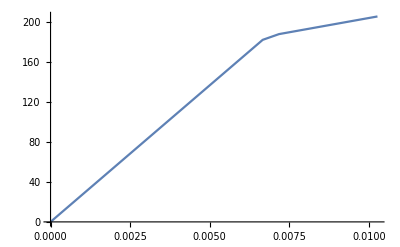

```mathematica
ListLinePlot[{{0,0},{χI*10^3, MRdI*10^-6},{χII*10^3, MRdII*10^-6}, {χIII*10^3, MRdIII*10^-6}}]
```

```mathematica
χI*10^3
 MRdI*10^-6
χII*10^3
MRdII*10^-6
 χIII*10^3 
MRdIII*10^-6
```

0.00281214

38.9156

0.00785452

203.375

0.0102693

205.692